```mathematica
ShowGraph5Least[amigo1]
```

-Graphics-294131

```mathematica
allGraphs5[amigo1,"parents"]
```

{29412,29404,29170,28684,27226,22852,9730}

```mathematica
Map[ShowGraph5Least,Flatten[allGraphs5[amigo1,"children"]]]
```

{-Graphics-294940,-Graphics-296020,-Graphics-294400,-Graphics-295510,-Graphics-294160,-Graphics-294460}

```mathematica
Map[ShowGraph5Least,Flatten[allGraphs5[amigo1,"parents"]]]
```

{-Graphics-294122,-Graphics-294042,-Graphics-291702,-Graphics-286842,-Graphics-272262,-Graphics-228522,-Graphics-97302}

```mathematica
allGraphs5[K5Key,"parents"]
```

{29523,29521,29515,29497,29443,29281,28795,27337,22963,9841}

```mathematica
Table[Graph[FormulaGraphReverse2[allGraphs5[k,"colofour"]],GraphHighlight->With[{g=FormulaGraphReverse2[allGraphs5[K5Key,"colofour"]]},Join[EdgeList[g],VertexList[g]]], GraphHighlightStyle->"Thick"],
{k,allGraphs5[K5Key,"parents"]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Labeled[Graph[FormulaGraphReverse2[allGraphs5[k,"colofour"]],GraphHighlight->With[{g=FormulaGraphReverse2[allGraphs5[amigo1,"colofour"]]},Join[EdgeList[g],VertexList[g]]], GraphHighlightStyle->"Thick"],ShowGraph5Least[k]],
{k,allGraphs5[amigo1,"parents"]}]
```

{-Graphics--Graphics-294122,-Graphics--Graphics-294042,-Graphics--Graphics-291702,-Graphics--Graphics-286842,-Graphics--Graphics-272262,-Graphics--Graphics-228522,-Graphics--Graphics-97302}

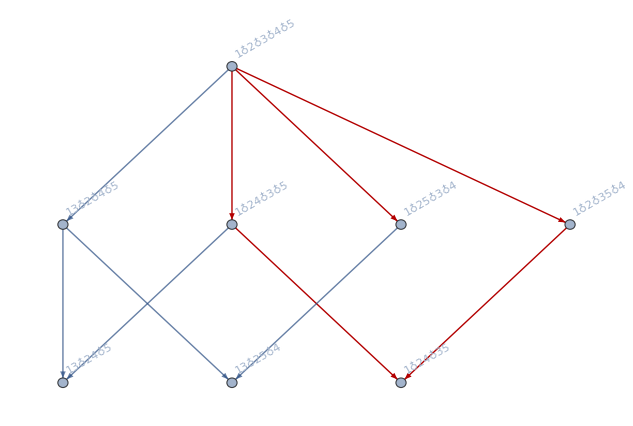

```mathematica
Graph[FormulaGraphReverse2[allGraphs5[22852,"colofour"]],GraphHighlight->EdgeList[FormulaGraphReverse2[allGraphs5[amigo1,"colofour"]]]]
```

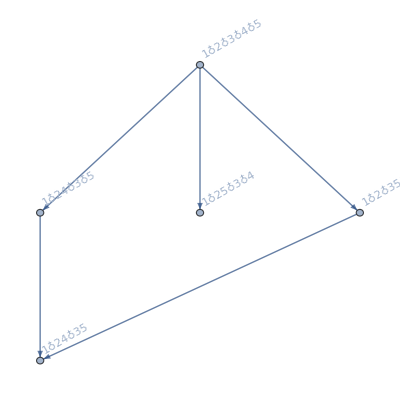

```mathematica
FormulaGraphReverse2[allGraphs5[amigo1,"colofour"]]
```

```mathematica
With[{key=lambdaKey},
Table[Labeled[Graph[FormulaGraphReverse2[allGraphs5[k,"colofour"]],GraphHighlight->With[{g=FormulaGraphReverse2[allGraphs5[key,"colofour"]]},Join[EdgeList[g],VertexList[g]]], GraphHighlightStyle->"Thick"],ShowGraph5Least[k]],
{k,allGraphs5[key,"parents"]}]
]
```

{-Graphics--Graphics-206645,-Graphics--Graphics-206565,-Graphics--Graphics-204225,-Graphics--Graphics-199365,-Graphics--Graphics-9825}

```mathematica
With[{key=lambdaKey},
Table[Labeled[Graph[FormulaGraphReverse2[allGraphs5[key,"colofour"]],GraphHighlight->With[{g=FormulaGraphReverse2[allGraphs5[k,"colofour"]]},Join[EdgeList[g],VertexList[g]]], GraphHighlightStyle->{"Dashed","Thick"}
, ImageSize->500],ShowGraph5Least[k]],
{k,Flatten[allGraphs5[key,"children"]]}]
]
```

{-Graphics--Graphics-272262,-Graphics--Graphics-359771,-Graphics--Graphics-228522,-Graphics--Graphics-316811,-Graphics--Graphics-207462,-Graphics--Graphics-230411,-Graphics--Graphics-206922,-Graphics--Graphics-208031,-Graphics--Graphics-206682,-Graphics--Graphics-272591}

```mathematica
With[{key=alfaKey},
Table[Labeled[Graph[FormulaGraphReverse2[allGraphs5[k,"colofour"]],GraphHighlight->With[{g=FormulaGraphReverse2[allGraphs5[key,"colofour"]]},Join[EdgeList[g],VertexList[g]]], GraphHighlightStyle->"Thick"],ShowGraph5Least[k]],
{k,allGraphs5[key,"parents"]}]
]
```

{-Graphics--Graphics-359762,-Graphics--Graphics-352452,-Graphics--Graphics-352452,-Graphics--Graphics-337812,-Graphics--Graphics-337812,-Graphics--Graphics-228551,-Graphics--Graphics-228522,-Graphics--Graphics-228462,-Graphics--Graphics-228433,-Graphics--Graphics-226121,-Graphics--Graphics-226093,-Graphics--Graphics-226033,-Graphics--Graphics-226005,-Graphics--Graphics-221262,-Graphics--Graphics-221174,-Graphics--Graphics-218833,-Graphics--Graphics-218747,-Graphics--Graphics-206682,-Graphics--Graphics-206653,-Graphics--Graphics-204253,-Graphics--Graphics-204225,-Graphics--Graphics-199393,-Graphics--Graphics-196965,-Graphics--Graphics-160512,-Graphics--Graphics-160512,-Graphics--Graphics-31721,-Graphics--Graphics-31693,-Graphics--Graphics-31633,-Graphics--Graphics-31605,-Graphics--Graphics-24433,-Graphics--Graphics-24347,-Graphics--Graphics-9853,-Graphics--Graphics-9825,-Graphics--Graphics-2565}

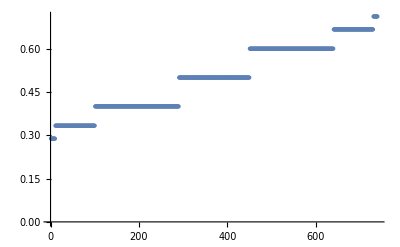

```mathematica
ListPlot[Table[Table[Length[ListofVars[allGraphs5[child,"colofour"]]]/Length[ListofVars[allGraphs5[k,"colofour"]]],{child,Flatten[allGraphs5[k,"children"]]}],{k,allGraphs5NullAtomKeys}]//Flatten//Sort,PlotRange->All]
```

```mathematica
With[{list=Flatten[Table[Table[Length[ListofVars[allGraphs5[child,"colofour"]]]/Length[ListofVars[allGraphs5[k,"colofour"]]],{child,Flatten[allGraphs5[k,"children"]]}],{k,allGraphs5NullAtomKeys}]]},
{Min[list],Max[list],Mean[list]}]
```

{15/52,37/52,1/2}

```mathematica
With[{list=Flatten[Table[Table[Length[ListofVars[allGraphs5[child,"colofour"]]]/Length[ListofVars[allGraphs5[k,"colofour"]]],{child,Flatten[allGraphs5[k,"children"]]}],{k,Keys[allGraphs5]}]]},
{Min[list],Max[list],Mean[list]}]
```

{1/7,6/7,1/2}

```mathematica
With[{list=Flatten[Table[Table[Length[ListofVars[allGraphs6[child,"colofour"]]]/Length[ListofVars[allGraphs6[k,"colofour"]]],{child,Flatten[allGraphs6[k,"children"]]}],{k,Keys[allGraphs6]}]]},
{Min[list],Max[list],Mean[list]}]
```

{1/10,9/10,1/2}

```mathematica
With[{list=Flatten[Table[Table[Length[ListofVars[allGraphs4[child,"colofour"]]]/Length[ListofVars[allGraphs4[k,"colofour"]]],{child,Flatten[allGraphs4[k,"children"]]}],{k,Keys[allGraphs4]}]]},
{Min[list],Max[list],Mean[list]}]
```

{1/5,4/5,1/2}

```mathematica
With[{list=Flatten[Table[Table[Length[ListofVars[allGraphs3[child,"colofour"]]]/Length[ListofVars[allGraphs3[k,"colofour"]]],{child,Flatten[allGraphs3[k,"children"]]}],{k,Keys[allGraphs3]}]]},
{Min[list],Max[list],Mean[list]}]
```

{1/3,2/3,1/2}

```mathematica
With[{list=Flatten[Table[Table[Length[ListofVars[allGraphs2[child,"colofour"]]]/Length[ListofVars[allGraphs2[k,"colofour"]]],{child,Flatten[allGraphs2[k,"children"]]}],{k,Keys[allGraphs2]}]]},
{Min[list],Max[list],Mean[list],list}]
```

{1/2,1/2,1/2,{1/2,1/2}}

```mathematica
Monitor[
Table[
With[{list=Flatten[Table[Table[Length[ListofVars[all[child,"colofour"]]]/Length[ListofVars[all[k,"colofour"]]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
{Min[list],Max[list],Mean[list]}]
,
{all,{allGraphs2,allGraphs3,allGraphs4,allGraphs5,allGraphs6}}
],Length[all]
]
```

{{1/2,1/2,1/2},{1/3,2/3,1/2},{1/5,4/5,1/2},{1/7,6/7,1/2},{1/10,9/10,1/2}}

```mathematica
Monitor[
Table[
With[{list=Flatten[Table[Table[Length[ListofVars[all[child,"colofourrealnull"]]]/Length[ListofVars[all[k,"colofourrealnull"]]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
{Min[list],Max[list],Mean[list]}]
,
{all,{allGraphs2,allGraphs3,allGraphs4,allGraphs5}}
],Length[all]
]
```

{{1,2,3/2},{1/2,2,67/48},{1/3,2,110881/87360},{4/17,2,6654817665382487/5860392282763200}}

```mathematica
FactorInteger[6654817665382487]
```

{{16097,1},{413419746871,1}}

```mathematica
FactorInteger[5860392282763200]
```

{{2,6},{3,2},{5,2},{7,1},{13,2},{17,2},{19,1},{31,1},{43,1},{47,1}}

```mathematica
Monitor[
Table[
With[{list=Flatten[Table[Table[Length[ListofVars[all[child,"colofourgenerator"]]]/Length[ListofVars[all[k,"colofourgenerator"]]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
{Min[list],Max[list],Mean[list]}]
,
{all,{allGraphs2,allGraphs3,allGraphs4,allGraphs5,allGraphs6}}
],Length[all]
]
```

{{1,1,1},{1,1,1},{1,1,1},{10/51,38,133122405310841/147524719141800}}

```mathematica
Monitor[
Table[
With[{list=Flatten[Table[Table[Length[ListofVars[all[child,"colofournull"]]]/Length[ListofVars[all[k,"colofournull"]]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
{Min[list],Max[list],Mean[list]}]
,
{all,{allGraphs2,allGraphs3,allGraphs4,allGraphs5}}
],Length[all]
]
```

{{1,2,3/2},{1/4,4,39/16},{1/14,14,26617/7840},{1/45,45,138347271981829/43989188980464}}

```mathematica
,,,
```